## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/fourier/"; 
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /home/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /home/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.334614 GB

seed file: /home/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: dtopa-latitude-5491,  MM v. 12.0.0 for Linux x86

date: Mar 4, 2020, time: 12:53:44

nb: /home/dantopa/Mathematica_files/nb/ert/rcs/fourier/amplitudes-02.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.334614 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

#### functions

#### substitutions

#### modules

## import

```mathematica
meanRCS=Import[dirData<>"rcs-values.dat"];
```

## data

### grab slice

```mathematica
σ=meanRCS[[1]];
m=Length[σ];
```

```mathematica
Mean[σ]
```

35.2488

```mathematica
Clear[σ];
σ=Table[
2Cos[2x]-3Sin[3x]
,{x,-π,π,180/π}]
```

{2}

```mathematica
σ=Table[
θ=k π/180;
2Cos[2θ]-3Sin[3θ]
,{k,360}];
m=Length[σ];
```

```mathematica
(* one degree *) 
Δθ=π/180;
```

```mathematica
a0=1/m∑_(k=1)^m σ[[k]]
Simplify[%]
```

1/360 (-2 (-1-√5)-2 (1-√5)-2 (-1+√5)-2 (1+√5))

0

### cosine terms

```mathematica
d=5;
```

```mathematica
a=Table[
Simplify[1/m∑_(k=1)^m σ[[k]]Cos[j k Δθ]]
,{j,d}]
```

{0,1,0,0,0}

```mathematica
b=Table[
1/m Simplify[∑_(k=1)^m σ[[k]]Sin[j k Δθ]]
,{j,d}];
```

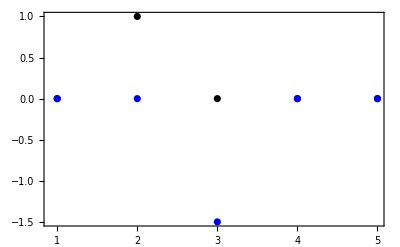

```mathematica
ListPlot[{a,b},
Frame->True,
PlotStyle->{Black,Blue},
PlotRange->All]
```

## compare

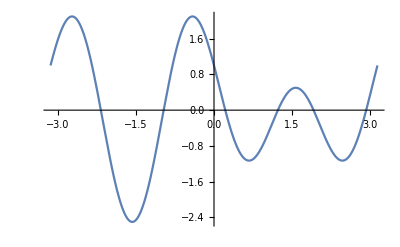

```mathematica
Plot[a0+Sum[a[[j]]Cos[j x]+b[[j]]Sin[j x],{j,d}],{x,-π,π}]
```

```mathematica
fit=Table[
θ=(k-180) π/180;
a0+Sum[a[[j]]Cos[j θ],{j,d}]
,{k,0,360}];
```

```mathematica
asymmetry=Table[
θ=(k-180) π/180;
Sum[b[[j]]Sin[j θ],{j,d}]
,{k,0,360}];
```

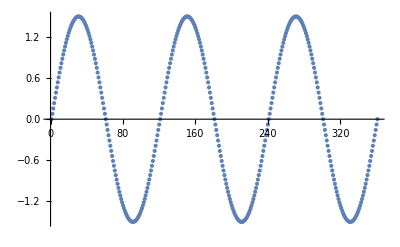

```mathematica
ListPlot[asymmetry]
```

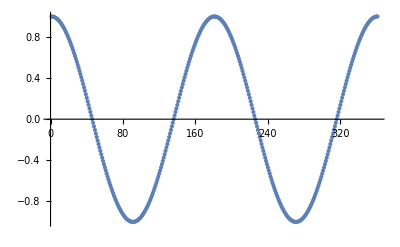

```mathematica
ListPlot[fit]
```

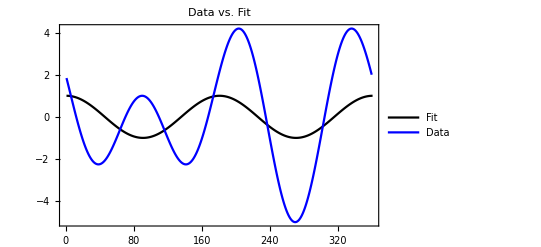

```mathematica
ListPlot[{fit,σ},
PlotStyle->{Black,Blue},
PlotLabel->"Data vs. Fit",
Joined->True,
Frame->True,
PlotLegends->{"Fit","Data"},
PlotRange->All]
```

```mathematica
ListPlot[fit-σ,
PlotLabel->"Residual Fit Error",
Frame->True]
```

Thread::tdlen: Objects of unequal length in {1+1/360 (-2 (-1+Times[«2»])-2 (1+Times[«2»])-2 (-1+Power[«2»])-2 (1+Power[«2»])),«49»,«311»}+{-2 Cos[π/90]+3 Sin[π/60],-2 Cos[π/45]+3 Sin[π/30],«47»,3/2+2 Sin[π/18],«310»} cannot be combined.

Thread::tdlen: Objects of unequal length in {-1.84177378530936,-1.681542710716688,-1.519740395615854,«46»,1.847296355333861,«310»}+{«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {-1.8417737853093599618461309912606246727974,-1.6815427107166880810268228968810156954968,«48»,«310»}+{«20»,«49»,«311»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

ListPlot::lpn: {-1.84177,-1.68154,-1.51974,-1.3568,-1.19316,«41»,2.02747,1.97241,1.91226,1.8473,«310»}+«1» is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[{-2 Cos[π/90]+3 Sin[π/60],-2 Cos[π/45]+3 Sin[π/30],-2 Cos[π/30]+3 Sin[π/20],354,-2 Cos[π/45]-3 Sin[π/30],-2 Cos[π/90]-3 Sin[π/60],-2}+{1},PlotLabel→…r,Frame→True]
 |  |  |  |

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```